```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
χ=x[[15]];
Growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
Starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
InvaderStarvation =  N[ts*-Bm/(Em*(Log[1-f0*M^(γ-1)] + Log[M/(M*(1+χ))]))]*(1+RandomReal[{-noise,noise}]);
Mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
Recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
InvaderRecovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(1+χ)*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
Maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
InvaderMaintenance = (ts*ef*B0*(M*(1+χ))^η)*(1+RandomReal[{-noise,noise}]);
Resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{Growth,Starvation,Mortality,Recovery,Maintenance,Resourcegrowth,InvaderStarvation,InvaderRecovery,InvaderMaintenance}
);
```

```mathematica
FEq =λ*F-σ*(1-R)*F +ρ* R * H;
HEq =σ*(1-R)*F - ρ* R*H - μ*H;

FIEq =λ*FI-σ2*(1-R)*FI +ρ2* R * HI;
HIEq =σ2*(1-R)*FI- ρ2* R*HI - μ*HI;

REq=α*R*(1-R) -(ρ*H + β*F +ρ2*HI + β2*FI )*R ;
```

```mathematica
Solutions=FullSimplify[Solve[{FEq==0,HEq==0,FIEq==0,HIEq==0,REq==0},{F,H,FI,HI,R}]]
Length[Solutions]
```

{{F→0,H→0,FI→0,HI→0,R→0},{F→0,H→0,FI→0,HI→0,R→1},{F→(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)),H→(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)),FI→0,HI→0,R→(μ (-λ+σ))/(λ ρ+μ σ)},{F→0,H→0,FI→(α λ μ (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2)),HI→(α λ^2 (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2)),R→(μ (-λ+σ2))/(λ ρ2+μ σ2)}}

4

```mathematica
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^4,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
Growth=RF[[1]];
Starvation=RF[[2]];
Mortality=RF[[3]];
Recovery=RF[[4]];
Maintenance=RF[[5]];
Resourcegrowth=RF[[6]];
InvaderStarvation = RF[[7]];
InvaderRecovery=RF[[8]];
InvaderMaintenance=RF[[9]];
```

```mathematica
SpSol=Solutions/.{α->Re[Resourcegrowth],λ->Re[Growth],σ->Re[Starvation],ρ->Re[Recovery],β->Re[Maintenance],μ->Re[Mortality],σ2->Re[InvaderStarvation],ρ2->Re[InvaderRecovery],β2->Re[InvaderMaintenance]};
```

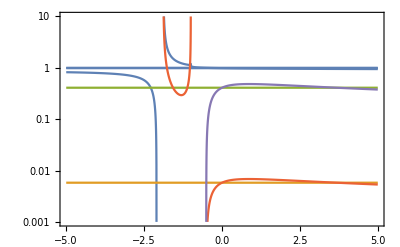

```mathematica
(*Row[{
LogPlot[{R/.SpSol,H/.SpSol,F/.SpSol,HI/.SpSol,FI/.SpSol},{chi,-.04,0.04},PlotRange->{0.3,0.5},Frame->True,AxesOrigin->{0,0},AspectRatio->2,ImageSize->135],*)
LogPlot[{R/.SpSol,H/.SpSol,F/.SpSol,HI/.SpSol,FI/.SpSol},{chi,-5,5},PlotRange->{0.001,10},Frame->True,AxesOrigin->{0,0},ImageSize->400](*}]*)
```

```mathematica
FSpec=F/.SpSol[[3]]
```

0.40967

```mathematica
FISpec=(FI/.SpSol[[4]])
```

(9.12565×10^-14 (3.59222×10^-6+5.72698×10^-7 Re[1/((-2.44256-3.14159 ⅈ)+Log[1.-12.8947 (1.+chi)^(1/4)])]))/((6.82522×10^-8 Re[(1+chi)^(3/4)]+2.90975×10^-14 Re[1/((-2.44256-3.14159 ⅈ)+Log[1.-12.8947 (1.+chi)^(1/4)])]) (-8.22903×10^-12 Re[1/(-0.123568+Log[1/(1.+chi)])]+2.90975×10^-14 Re[1/((-2.44256-3.14159 ⅈ)+Log[1.-12.8947 (1.+chi)^(1/4)])]))

```mathematica
Solve[FSpec==FISpec,chi]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

There are 2 coexistence points...